## Probando vainas

```mathematica
Subscript[r, 0,0]=1;KroneckerProduct[DiagonalMatrix[Table[Subscript[r, i,0],{i,0,3}]],DiagonalMatrix[Table[Subscript[r, 0,j],{j,0,3}]]]//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | r_(0,1) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | r_(0,2) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | r_(0,3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | r_(1,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | r_(0,1) r_(1,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | r_(0,2) r_(1,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,3) r_(1,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(2,0) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,1) r_(2,0) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,2) r_(2,0) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,3) r_(2,0) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(3,0) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,1) r_(3,0) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,2) r_(3,0) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | r_(0,3) r_(3,0))

```mathematica
KroneckerProduct[DiagonalMatrix[{1/4 (1+Subscript[r, 1]-Subscript[r, 2]-Subscript[r, 3]),1/4 (1-Subscript[r, 1]-Subscript[r, 2]+Subscript[r, 3]),1/4 (1-Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 3]),1/4 (1+Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 3])}],DiagonalMatrix[{1/4 (1+Subscript[r, 1]-Subscript[r, 2]-Subscript[r, 3]),1/4 (1-Subscript[r, 1]-Subscript[r, 2]+Subscript[r, 3]),1/4 (1-Subscript[r, 1]+Subscript[r, 2]-Subscript[r, 3]),1/4 (1+Subscript[r, 1]+Subscript[r, 2]+Subscript[r, 3])}]]//MatrixForm
```

(1/16 (1+r_1-r_2-r_3)^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1/16 (1+r_1-r_2-r_3) (1-r_1-r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1/16 (1+r_1-r_2-r_3) (1-r_1+r_2-r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1/16 (1+r_1-r_2-r_3) (1+r_1+r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1/16 (1+r_1-r_2-r_3) (1-r_1-r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1-r_2+r_3)^2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1+r_2-r_3) (1-r_1-r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1-r_2+r_3) (1+r_1+r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1+r_1-r_2-r_3) (1-r_1+r_2-r_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1+r_2-r_3) (1-r_1-r_2+r_3) | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1+r_2-r_3)^2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1+r_2-r_3) (1+r_1+r_2+r_3) | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1+r_1-r_2-r_3) (1+r_1+r_2+r_3) | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1-r_2+r_3) (1+r_1+r_2+r_3) | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1-r_1+r_2-r_3) (1+r_1+r_2+r_3) | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/16 (1+r_1+r_2+r_3)^2)

#### Por aquí se empieza a ver cuál es la forma general del superoperador de los PCE:

```mathematica
KroneckerProduct[DiagonalMatrix[PCE[Table[Subscript[r^a, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^b, i],{i,0,3}]]//Reshuffle//Eigenvalues]]*4//Reshuffle//Tr//FullSimplify
```

1/4 ((r^a)_0 (r^b)_0+(r^a)_1 (r^b)_1+(r^a)_2 (r^b)_2+(r^a)_3 (r^b)_3)

```mathematica
twoQubits[[2]]//Length
```

15

```mathematica
MatrixForm[#,TableSpacing->{2,2}]&/@ReplacePart[twoQubits[[2]],{Position[twoQubits[[2]],1]->1,Position[twoQubits[[2]],0]->"×"}]
```

{(1 | 1 | × | ×
1 | 1 | × | ×
× | × | 1 | 1
× | × | 1 | 1),(1 | × | × | 1
1 | × | × | 1
× | 1 | 1 | ×
× | 1 | 1 | ×),(1 | × | 1 | ×
1 | × | 1 | ×
× | 1 | × | 1
× | 1 | × | 1),(1 | 1 | 1 | 1
1 | 1 | 1 | 1
× | × | × | ×
× | × | × | ×),(1 | 1 | × | ×
× | × | 1 | 1
× | × | 1 | 1
1 | 1 | × | ×),(1 | × | × | 1
× | 1 | 1 | ×
× | 1 | 1 | ×
1 | × | × | 1),(1 | × | 1 | ×
× | 1 | × | 1
× | 1 | × | 1
1 | × | 1 | ×),(1 | 1 | 1 | 1
× | × | × | ×
× | × | × | ×
1 | 1 | 1 | 1),(1 | 1 | × | ×
× | × | 1 | 1
1 | 1 | × | ×
× | × | 1 | 1),(1 | × | × | 1
× | 1 | 1 | ×
1 | × | × | 1
× | 1 | 1 | ×),(1 | × | 1 | ×
× | 1 | × | 1
1 | × | 1 | ×
× | 1 | × | 1),(1 | 1 | 1 | 1
× | × | × | ×
1 | 1 | 1 | 1
× | × | × | ×),(1 | 1 | × | ×
1 | 1 | × | ×
1 | 1 | × | ×
1 | 1 | × | ×),(1 | × | × | 1
1 | × | × | 1
1 | × | × | 1
1 | × | × | 1),(1 | × | 1 | ×
1 | × | 1 | ×
1 | × | 1 | ×
1 | × | 1 | ×)}

```mathematica
𝒫𝒞ℰ=(DiagonalMatrix[#//Flatten]&/@twoQubits[[2]]);TwoQBoard/@twoQubits[[2]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Log[2,]
```

Log[3]/Log[2]

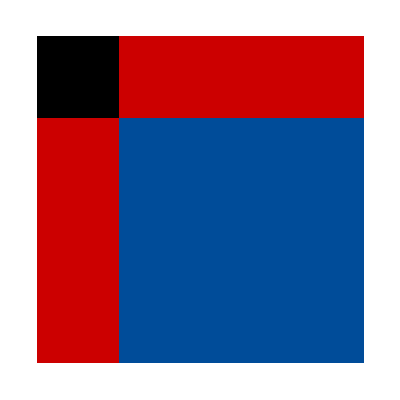

```mathematica
TwoQBoard@ConstantArray[1,{4,4}]
```

```mathematica
ρ=ConstantArray[1,16]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
TwoQBoard[ArrayReshape[#,{4,4}]]&/@{𝒫𝒞ℰ[[4]].𝒫𝒞ℰ[[1]].ρ,𝒫𝒞ℰ[[11]].𝒫𝒞ℰ[[1]].ρ,𝒫𝒞ℰ[[8]].𝒫𝒞ℰ[[4]].ρ,𝒫𝒞ℰ[[5]].𝒫𝒞ℰ[[4]].ρ,𝒫𝒞ℰ[[11]].𝒫𝒞ℰ[[3]].ρ}
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

1. 3 bloch locales
2. 2 bloch locales
3. 1 bloch locales
4. 0 bloch locales

```mathematica
PCE[Table[Subscript[r, i,j],{i,0,3},{j,0,3}]//Flatten]//MatrixForm
```

(1/4+(r_(0,3))/4+(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4+(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4-(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4-(r_(3,0))/4+(r_(3,3))/4
0 | (r_(0,1))/4+(r_(0,2))/4+(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4+(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4-(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4-(r_(3,1))/4+(r_(3,2))/4 | 0
0 | 0 | (r_(1,0))/4+(r_(1,3))/4+(r_(2,0))/4+(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4-(r_(1,3))/4+(r_(2,0))/4-(r_(2,3))/4 | (r_(1,0))/4+(r_(1,3))/4-(r_(2,0))/4-(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4-(r_(1,3))/4-(r_(2,0))/4+(r_(2,3))/4 | 0 | 0
0 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4+(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4+(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4-(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4-(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | 0
0 | (r_(0,1))/4-(r_(0,2))/4+(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4+(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4-(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4-(r_(3,1))/4-(r_(3,2))/4 | 0
1/4-(r_(0,3))/4+(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4+(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4-(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4-(r_(3,0))/4-(r_(3,3))/4
0 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4+(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4+(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4-(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4-(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | 0
0 | 0 | (r_(1,0))/4-(r_(1,3))/4+(r_(2,0))/4-(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4+(r_(1,3))/4+(r_(2,0))/4+(r_(2,3))/4 | (r_(1,0))/4-(r_(1,3))/4-(r_(2,0))/4+(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4+(r_(1,3))/4-(r_(2,0))/4-(r_(2,3))/4 | 0 | 0
0 | 0 | (r_(1,0))/4+(r_(1,3))/4-(r_(2,0))/4-(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4-(r_(1,3))/4-(r_(2,0))/4+(r_(2,3))/4 | (r_(1,0))/4+(r_(1,3))/4+(r_(2,0))/4+(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4-(r_(1,3))/4+(r_(2,0))/4-(r_(2,3))/4 | 0 | 0
0 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4-(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4-(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4+(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4+(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | 0
1/4+(r_(0,3))/4-(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4-(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4+(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4+(r_(3,0))/4-(r_(3,3))/4
0 | (r_(0,1))/4+(r_(0,2))/4-(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4-(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4+(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4+(r_(3,1))/4-(r_(3,2))/4 | 0
0 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4-(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4-(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4-(r_(1,2))/4+(r_(2,1))/4-(r_(2,2))/4 | 0 | 0 | (r_(1,1))/4+(r_(1,2))/4+(r_(2,1))/4+(r_(2,2))/4 | 0 | 0 | 0
0 | 0 | (r_(1,0))/4-(r_(1,3))/4-(r_(2,0))/4+(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4+(r_(1,3))/4-(r_(2,0))/4-(r_(2,3))/4 | (r_(1,0))/4-(r_(1,3))/4+(r_(2,0))/4-(r_(2,3))/4 | 0 | 0 | 0 | 0 | (r_(1,0))/4+(r_(1,3))/4+(r_(2,0))/4+(r_(2,3))/4 | 0 | 0
0 | (r_(0,1))/4-(r_(0,2))/4-(r_(3,1))/4+(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4-(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | 0 | 0 | 0 | 0 | (r_(0,1))/4-(r_(0,2))/4+(r_(3,1))/4-(r_(3,2))/4 | 0 | 0 | (r_(0,1))/4+(r_(0,2))/4+(r_(3,1))/4+(r_(3,2))/4 | 0
1/4-(r_(0,3))/4-(r_(3,0))/4+(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4-(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4-(r_(0,3))/4+(r_(3,0))/4-(r_(3,3))/4 | 0 | 0 | 0 | 0 | 1/4+(r_(0,3))/4+(r_(3,0))/4+(r_(3,3))/4)

```mathematica
(PCE[#//Flatten]//Reshuffle//Eigenvectors)&/@ToExpression[twoQ][[2;;]]
```

{{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,1,0,0,1,0,0,0,0,0,0,1,0,0,1,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,-1,0,0,1,0,0,0,0,0,0,-1,0,0,1,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1},{1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,1,0,0,0,0,1,1,0,0,0,0,1,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,0,1,0,0,1,0,0,1,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,0,-1,0,0,1,0,0,-1,0,0,1,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,-1,0,0,0,0,1,-1,0,0,0,0,1,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,-1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,-1,0,0,0,0,-1,1,0,0,0,0,1,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,-1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,0,-1,0,0,-1,0,0,1,0,0,1,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,-1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,0,1,0,0,-1,0,0,-1,0,0,1,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,-1,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,0,1,0,0,0,0,-1,-1,0,0,0,0,1,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,-1,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1},{1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,-1,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,-1,0,0,-1,0,0,0,0,0,0,1,0,0,1,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,-1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,1,0,0,0,0,1,0,0,0,0,1},{0,1,0,0,-1,0,0,0,0,0,0,-1,0,0,1,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,-1,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{-1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0}},{{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0},{-1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,-1,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
KroneckerProduct[DiagonalMatrix[PCE[Table[Subscript[r^a, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^b, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^c, i],{i,0,3}]]//Reshuffle//Eigenvalues]]*8//Reshuffle//MatrixForm
```

(1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1-(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1+(r^a)_2-(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0-(r^a)_1-(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1-(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1+(r^b)_2-(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3)
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0-(r^b)_1-(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1-(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1+(r^c)_2-(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0-(r^c)_1-(r^c)_2+(r^c)_3) | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1/64 ((r^a)_0+(r^a)_1+(r^a)_2+(r^a)_3) ((r^b)_0+(r^b)_1+(r^b)_2+(r^b)_3) ((r^c)_0+(r^c)_1+(r^c)_2+(r^c)_3))

```mathematica
KroneckerProduct[DiagonalMatrix[PCE[Table[Subscript[r^a, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^b, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^c, i],{i,0,3}]]//Reshuffle//Eigenvalues],DiagonalMatrix[PCE[Table[Subscript[r^d, i],{i,0,3}]]//Reshuffle//Eigenvalues]]*16//Reshuffle//MatrixForm
```

#### Probable explicación a los eigenvalores: producto tensorial entre matrices de Choi y luego considerar que, en general los coeficientes no son separables

#### 1 qubit-PCE Choi matrix’s eigenvectors are the Pauli matrices (Kraus operators)

```mathematica
PCE[Table[Subscript[r, i],{i,0,3}]]//Reshuffle//Eigensystem
```

{{1/4 (1+r_1-r_2-r_3),1/4 (1-r_1-r_2+r_3),1/4 (1-r_1+r_2-r_3),1/4 (1+r_1+r_2+r_3)},{{0,1,1,0},{-1,0,0,1},{0,-1,1,0},{1,0,0,1}}}

```mathematica
15*15
```

225